## Hopfield model for neuronal network

## Define 10 patterns ( numbers 0 to 9) on the 10 by 10 grid.

```mathematica
Clear[HH,OO,PP,FF,II,EE,LL,DD]

HH =     {{0,0,0,0,0,0,0,0,0,0},
           {0,1,1,0,0,0,0,1,1,0},
           {0,1,1,0,0,0,0,1,1,0},
           {0,1, 1,0,0,0,0,1,1,0},
           {0,1,1,1,1,1,1,1,1,0},
	{0,1,1,1,1,1,1,1,1,0},
           {0,1,1,0,0,0,0,1,1,0},
           {0,1,1,0,0,0,0,1,1,0},
           {0,1,1,0,0,0,0,1,1,0},
           {0,0,0,0,0,0,0,0,0,0} };


  OO =   {{0,0,0,0,0,0,0,0,0,0},
           {0,0,0,1,1,1,1,0,0,0},
           {0,1,1,1,1,1,1,1,0,0},
           {0,1, 1,0,0,0,0,1,1,0},
           {0,1, 1,0,0,0,0,1,1,0},
	 {0,1, 1,0,0,0,0,1,1,0},
            {0,1, 1,0,0,0,0,1,1,0},
            {0,1, 1,0,0,0,0,1,1,0},
            {0,0,0,1,1,1,1,0,0,0},
           {0,0,0,0,0,0,0,0,0,0} };

PP =        {{0,0,0,0,0,0,0,0,0,0},
           {0,1,1,1,1,1,1,0,0,0},
	{0,1,1,1,1,1,1,1,0,0},
           {0,1, 1,0,0,0,0,1,1,0},
           {0,1,1,1,1,1,1,1,0,0},
	{0,1,1,1,1,1,1,1,0,0},
           {0,1,1,0,0,0,0,0,0,0},
           {0,1,1,0,0,0,0,0,0,0},
           {0,1,1,0,0,0,0,0,0,0},
           {0,0,0,0,0,0,0,0,0,0} };


FF =     {{0,0,0,0,0,0,0,0,0,0},
           {0,1,1,1,1,1,1,1,1,0},
	{0,1,1,1,1,1,1,1,1,0},
           {0,1, 1,0,0,0,0,0,0,0},
           {0,1,1,1,1,1,1,1,1,0},
	{0,1,1,1,1,1,1,1,1,0},
           {0,1,1,0,0,0,0,0,0,0},
           {0,1,1,0,0,0,0,0,0,0},
           {0,1,1,0,0,0,0,0,0,0},
           {0,0,0,0,0,0,0,0,0,0} };

II=      {{0,0,0,0,0,0,0,0,0,0},
          {0,1,1,1,1,1,1,1,1,0},
	{0,1,1,1,1,1,1,1,1,0},
           {0,0,0,0,1, 1,0,0,0,0},
           {0,0,0,0,1, 1,0,0,0,0},
	{0,0,0,0,1, 1,0,0,0,0},
           {0,0,0,0,1, 1,0,0,0,0},
           {0,1,1,1,1,1,1,1,1,0},
	{0,1,1,1,1,1,1,1,1,0},
           {0,0,0,0,0,0,0,0,0,0} };

EE =    {{0,0,0,0,0,0,0,0,0,0},
          {0,1,1,1,1,1,1,1,1,0},
	{0,1,1,1,1,1,1,1,1,0},
             {0,1,1,0,0,0,0,0,0,0},
            {0,1,1,1,1,1,1,1,1,0},
	{0,1,1,1,1,1,1,1,1,0},
           {0,1,1,0,0,0,0,0,0,0},
           {0,1,1,1,1,1,1,1,1,0},
	{0,1,1,1,1,1,1,1,1,0},
           {0,0,0,0,0,0,0,0,0,0} };

LL =     {{0,0,0,0,0,0,0,0,0,0},
           {0,1,1,0,0,0,0,0,0,0},
           {0,1,1,0,0,0,0,0,0,0},
           {0,1, 1,0,0,0,0,0,0,0},
           {0,1,1,0,0,0,0,0,0,0},
	{0,1,1,0,0,0,0,0,0,0},
           {0,1,1,0,0,0,0,0,0,0},
           {0,1,1,1,1,1,1,1,1,0},
	{0,1,1,1,1,1,1,1,1,0},
           {0,0,0,0,0,0,0,0,0,0} };

DD =      {{0,0,0,0,0,0,0,0,0,0},
           {0,1,1,1,1,1,1,1,0,0},
           {0,1,1,1,1,1,1,1,1,0},
           {0,1, 1,0,0,0,0,1,1,0},
           {0,1, 1,0,0,0,0,1,1,0},
           {0,1, 1,0,0,0,0,1,1,0},
           {0,1, 1,0,0,0,0,1,1,0},
	{0,1,1,1,1,1,1,1,0,0},
           {0,1,1,1,1,1,1,0,0,0},      
           {0,0,0,0,0,0,0,0,0,0} };
```

## Define “plot” function to show the patterns to bare eyes.

```mathematica
Clear[plot];

plot[s_] := Module[{sflp = s},
L = Length[s];
For[i = 1, i ≤ L, ++i,
sflp[[i]] = 1- s[[L-i + 1]]
];
ListDensityPlot[sflp]
]

plot[EE]
plot[OO]
```

-Graphics-

-Graphics-

## (1) tosign[x] maps (1,0) binary into Ising values (+1,-1). (2) toarray[s] converts the binary array (100 dimensional vector here) into Ising array. (3) topattern[s] converts array into grid pattern. The weight matrix between all nodes takes the form W[i,j] = p[i] p[j]. One can sum over contributions from all patterns. The default choice here only contains three patterns (one, two, three). One can also include all patterns and other possible combinations.

```mathematica
Clear[tosign,toarray,topattern];
Clear[wmatrix,W];

tosign[0] := -1; tosign[x_] := 1 /; x>0;
toarray[s_] := Map[tosign, Flatten[s]]
topattern[s_] := Module[{},
Table[s[[i+10*(j-1)]], {j,10},{i,10}]
]

wmatrix[lett_] := Module[{p},
p = Flatten[lett];
p= Map[tosign, p];
Outer[Times,p,p]
] 

(* The Hopfield network only contains three patterns: zero, one, two. *)
W = (  wmatrix[EE]+wmatrix[OO])/10.0;

(* The Hopfield network only contains all ten patterns. *)
(*W = (  wmatrix[zero]+wmatrix[one] + wmatrix[two] + wmatrix[three] + wmatrix[four] + wmatrix[five] + wmatrix[six] + wmatrix[seven] + wmatrix[eight] + wmatrix[nine])/10.0;*)
```

## Now we implement n-step Hopfield dynamics for the input signal sin with the wieght matrix W -- hopfield[n,W,sin].

```mathematica
Clear[hopfield];

hopfield[n_, W_, sin_] := Module[{s = sin},
L = Length[W];
Do[
  i = Ceiling[L * Random[]];
   s[[i]] = Sign[ W[[i]].s],
{n}];
s
]
```

## The input signal sin consists of the input pattern pin and some random noise (characterized by the parameter noise between 0 and 1.)

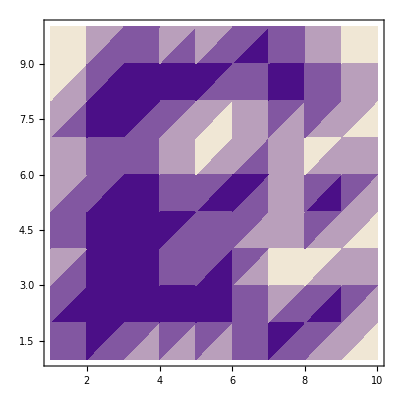

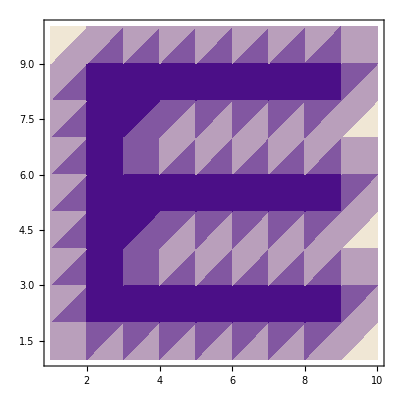

```mathematica
Clear[pin,noise];
Clear[sin,sout];

pin=EE;
noise=0.1;
sin = Table[If[Random[] < noise, 1-pin[[i,j]], pin[[i,j]]],{i,1,10},{j,1,10}];
plot[sin]

sout = hopfield[1000, W,toarray[sin]];
plot[topattern[sout]]
```